Abs[1-fs/f]

(-1+fs/f)^o Abs[1-fs/f]

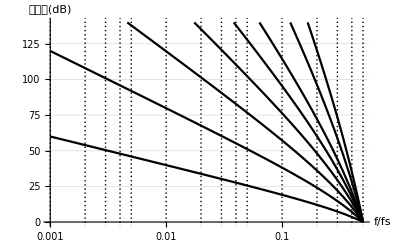

```mathematica
Gzoh[Ω_]:=Abs[Sin[Ω/2]/(Ω/2)];
Gratdac[fn_,fs_]:=Gzoh[2π f/fs]/Gzoh[2π(1-f/fs)];
FullSimplify[Gratdac[f,fs]]
Gratfil[f_,fs_,order_]:=((fs-f)/f)^order;
Grattol[f_,fs_,order_]:=Gratdac[f,fs]*Gratfil[f,fs,order];
FullSimplify[Grattol[f,fs,o]]
LogLinearPlot[20*Log10[Grattol[f,1,{0,1,2,3,4,5,7,9}]],{f,0.001,0.5},PlotTheme->"Monochrome",Ticks->{{0.001,0.002,0.005,0.01,0.02,0.05,0.1,0.2,0.5}, Automatic},PlotRange->{{0.001,0.5+0.00001},{0,140}},GridLines->{{0.001,0.002,0.003,0.004,0.005,0.01,0.02,0.03,0.04,0.05,0.1,0.2,0.3,0.4,0.5}, Automatic},AxesLabel->{Style["f/fs",FontFamily->"Times",FontSlant->Italic,FontSize->12],Style["信镜比(dB)",FontFamily->"Times",FontSize->12]}]
```

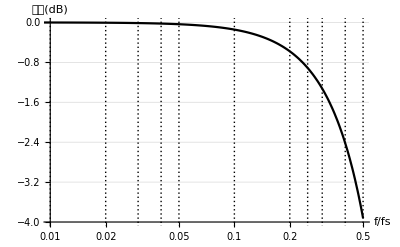

```mathematica
LogLinearPlot[20*Log10[Gzoh[2π f]],{f,0.001,0.5},PlotTheme->"Monochrome",Ticks->{{0.01,0.02,0.05,0.1,0.2,0.5}, Automatic},PlotRange->{{0.01,0.5+0.00001},{-4,0}},GridLines->{{0.01,0.02,0.03,0.04,0.05,0.1,0.2,0.3,0.4,0.5}, Automatic},AxesLabel->{Style["f/fs",FontFamily->"Times",FontSlant->Italic,FontSize->12],Style["增益(dB)",FontFamily->"Times",FontSize->12]},AxesOrigin->{0.01,-4}]
```